```mathematica
Quiet@Remove["Global`*"];
eqns = {2x+y == 7, x-y ==11};
sol = Solve[eqns, {x,y}][[1]]
Print["x= ",x/.sol, " y= ", y/.sol]
```

{x→6,y→-5}

x= 6 y= -5

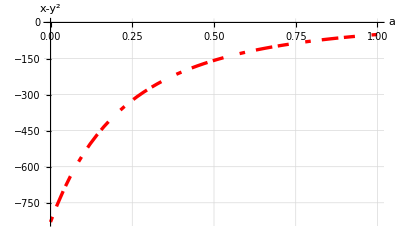

plot.png

```mathematica
eqns = {2x+y == 7*(a-1), x-a*y ==11};
sol = Solve[eqns, {x,y}][[1]];
exprToBePrinted =x - y^2 /.sol;
Plot[exprToBePrinted, {a,0,1}, AxesLabel->{"a", "x-y^2"}, PlotStyle->{Red, Thickness[0.006], Dashing[{0.01, 0.02,0.03}]}, GridLines-> {Automatic}]
Export["plot.png",plot, ImageResolution-> 300]
```

1/2 (-1-a-√((1+a)^2-4/(1+a^2)))

1/2 (-1-a+√((1+a)^2-4/(1+a^2)))

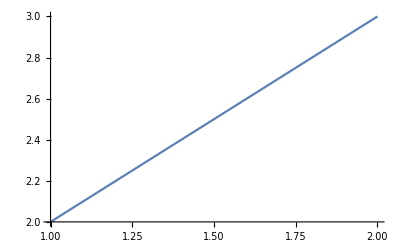

```mathematica
Quiet@Remove["Global`*"];
eqn = x^2 + (a+1)*x + 1/(1+a^2) == 0;
sol = Solve[eqn, x];
x1 = x/.sol[[1]]
x2 = x/.sol[[2]]
Plot[Abs[x1] + Abs[x2],{a, 1, 2}]
```

{3 y[t]+2 y'[t]+y''[t]==t Sin[2 t],y[0]==0,y'[0]==1}

-1/578 ⅇ^-t (88 Cos[√2 t]-88 ⅇ^t Cos[t]^2 Cos[√2 t]^2+136 ⅇ^t t Cos[t]^2 Cos[√2 t]^2-248 ⅇ^t Cos[t] Cos[√2 t]^2 Sin[t]+68 ⅇ^t t Cos[t] Cos[√2 t]^2 Sin[t]+88 ⅇ^t Cos[√2 t]^2 Sin[t]^2-136 ⅇ^t t Cos[√2 t]^2 Sin[t]^2-189 √2 Sin[√2 t]-88 ⅇ^t Cos[t]^2 Sin[√2 t]^2+136 ⅇ^t t Cos[t]^2 Sin[√2 t]^2-248 ⅇ^t Cos[t] Sin[t] Sin[√2 t]^2+68 ⅇ^t t Cos[t] Sin[t] Sin[√2 t]^2+88 ⅇ^t Sin[t]^2 Sin[√2 t]^2-136 ⅇ^t t Sin[t]^2 Sin[√2 t]^2)

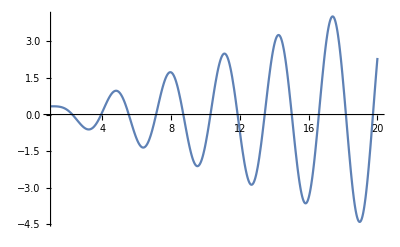

```mathematica
Quiet@Remove["Global`*"];
eqn = {y''[t]+2y'[t] + 3y[t] == t*Sin[2t], y[0]==0, y'[0] ==1}
sol = DSolve[eqn, y[t], t][[1]];
result = y[t]/.sol
Plot[result, {t,1,20}]
```

```mathematica
tStart = 23.5
t0 =t/.FindRoot[result ==5, {t, tStart}]
```

23.5

23.4556

```mathematica
t0 =t/.FindRoot[result==5,{t,tStart}]
Print["t0 = ", t0]
```

23.4556

t0 = 23.4556

{x1'[t]==Sin[2 t]-3 x1[t]+x2[t],x2'[t]==x1[t]-7 x2[t],x1[0]==1,x2[0]==2}

{x1[t]→1/328 ⅇ^(-5 t-√5 t-(-5+√5) t) (191 ⅇ^((-5+√5) t)-143 √5 ⅇ^((-5+√5) t)+191 ⅇ^(2 √5 t+(-5+√5) t)+143 √5 ⅇ^(2 √5 t+(-5+√5) t)-54 ⅇ^(2 √5 t) Cos[2 t]+76 ⅇ^(2 √5 t) Sin[2 t]),x2[t]→-1/328 ⅇ^(-5 t-√5 t-(-5+√5) t) (-333 ⅇ^((-5+√5) t)-95 √5 ⅇ^((-5+√5) t)-333 ⅇ^(2 √5 t+(-5+√5) t)+95 √5 ⅇ^(2 √5 t+(-5+√5) t)+10 ⅇ^(2 √5 t) Cos[2 t]-8 ⅇ^(2 √5 t) Sin[2 t])}

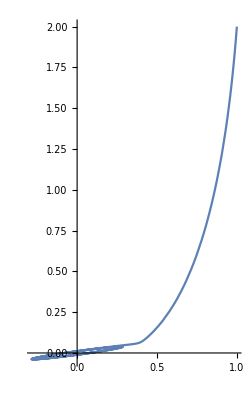

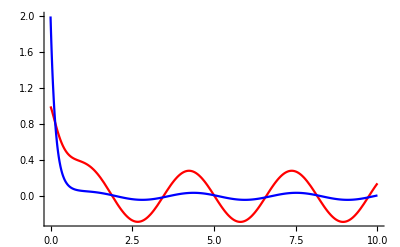

```mathematica
Quiet@Remove["Global`*"]
eqn = {x1'[t] == -3x1[t] + x2[t] + Sin[2t], x2'[t] == x1[t] - 7x2[t], x1[0] ==1, x2[0]==2}
sol = DSolve[eqn, {x1[t], x2[t]}, t][[1]]
ParametricPlot[{x1[t], x2[t]}/.sol, {t,0,10}, PlotRange->All]
Plot[Evaluate[{x1[t], x2[t]}/.sol], {t,0,10}, PlotRange->All, PlotStyle->{Red, Blue}]
```